#### This is the system I have in mind. The three wheels roll without slipping. The white dot at the center of the middle link marks the spot that I consider to have coordinates (x, y).

#### First, let’s derive the equations of motion from the velocity constraints.

```mathematica
bodyWheelPosition = {x[t], y[t]};
```

```mathematica
tailWheelPosition = bodyWheelPosition - {ρ Cos[θ[t]], ρ Sin[θ[t]]} - {ρ Cos[θ[t] - ψ[t]], ρ Sin[θ[t] - ψ[t]]};
```

```mathematica
headWheelPosition = bodyWheelPosition + {ρ Cos[θ[t]], ρ Sin[θ[t]]} + {ρ Cos[θ[t] + ϕ[t]], ρ Sin[θ[t] + ϕ[t]]};
```

```mathematica
bodyWheelVelocity = D[bodyWheelPosition, t];
```

```mathematica
tailWheelVelocity = D[tailWheelPosition, t];
```

```mathematica
headWheelVelocity = D[headWheelPosition, t];
```

```mathematica
bodyConstraint = bodyWheelVelocity.{- Sin[θ[t]], Cos[θ[t]]} == 0;
```

```mathematica
tailConstraint = tailWheelVelocity.{- Sin[θ[t] - ψ[t]], Cos[θ[t] - ψ[t]]} == 0;
```

```mathematica
headConstraint = headWheelVelocity.{- Sin[θ[t] + ϕ[t]], Cos[θ[t] + ϕ[t]]} == 0;
```

```mathematica
vectorComprisingxDotyDotAndθdot = {x'[t], y'[t], θ'[t]} /. Solve[{bodyConstraint, tailConstraint, headConstraint}, {x'[t], y'[t], θ'[t]}] // FullSimplify // Flatten;
```

```mathematica
equationsOfMotion := MapThread[Equal, {{ψ'[t], ϕ'[t], x'[t], y'[t], θ'[t]}, {ψdotInput, ϕdotInput}~Join~vectorComprisingxDotyDotAndθdot}];
```

#### Let's see what the equations of motion look like.

```mathematica
equationsOfMotion// MatrixForm  // OutputForm
```

ψ'[t] == ψdotInput



ϕ'[t] == ϕdotInput

         ρ Cos[θ[t]] ((1 + Cos[ψ[t]]) ϕ'[t] + (1 + Cos[ϕ[t]]) ψ'[t])
x'[t] == -----------------------------------------------------------
                  Sin[ϕ[t]] + Sin[ϕ[t] - ψ[t]] - Sin[ψ[t]]

         ρ Sin[θ[t]] ((1 + Cos[ψ[t]]) ϕ'[t] + (1 + Cos[ϕ[t]]) ψ'[t])
y'[t] == -----------------------------------------------------------
                  Sin[ϕ[t]] + Sin[ϕ[t] - ψ[t]] - Sin[ψ[t]]

            Sin[ψ[t]] ϕ'[t] + Sin[ϕ[t]] ψ'[t]
θ'[t] == ----------------------------------------
         Sin[ϕ[t]] + Sin[ϕ[t] - ψ[t]] - Sin[ψ[t]]

#### Now let’s definite initial conditions for our simulation, and construct piecewise constant functions of time for ψdotInput and ϕdotInput, from Jack’s CSV file. Each row in Jack’s file contains one value each for x, y, θ, ψ, ϕ, ψdot, and ϕdot, in that order.

```mathematica
jackData = Import["~/Downloads/Trial 1 th rollout 2019-05-15114913.021094.csv", "CSV"];
```

```mathematica
initialConditions = MapThread[Equal, {{x[0], y[0], θ[0], ψ[0], ϕ[0]}, Take[jackData[[1]], 5]}]
```

{x[0]==0,y[0]==0,θ[0]==0,ψ[0]==-0.785398,ϕ[0]==0.785398}

```mathematica
decisionTimes = .25 Range[200];
```

```mathematica
angleRates = Take[#, -2]& /@ jackData;
```

```mathematica
jacksψdots= Piecewise[Table[{angleRates[[i, 1]], t ≤ decisionTimes[[i]]}, {i, 1, 200}]];
```

```mathematica
jacksϕdots = Piecewise[Table[{angleRates[[i, 2]], t ≤ decisionTimes[[i]]}, {i, 1, 200}]];
```

```mathematica
solution = NDSolve[{equationsOfMotion /. {ρ -> 1 , ψdotInput -> jacksψdots, ϕdotInput -> jacksϕdots}, initialConditions}, {x[t], y[t], θ[t], ϕ[t], ψ[t]}, {t, 0, 50}];
```

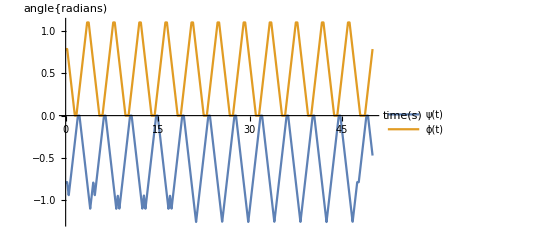

```mathematica
Plot[Evaluate[{ψ[t], ϕ[t]} /. solution], {t, 0, 50}, AxesLabel -> {"time(s)", "angle{radians)"}, LabelStyle -> Medium, PlotLegends -> {ψ[t], ϕ[t]}]
```

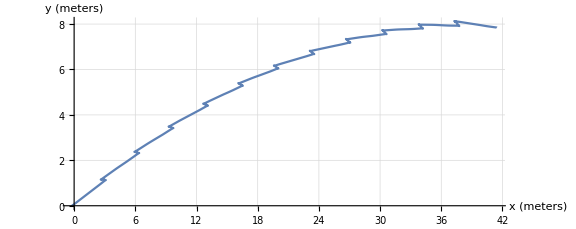

```mathematica
ParametricPlot[{x[t], y[t]} /. solution, {t, 0, 50}, GridLines -> Automatic, AxesLabel -> {"x (meters)", "y (meters)"}, LabelStyle -> Medium, ImageSize -> Large]
```